## Schrodinger Equation — Theory

Rather than go through the theory abstractly, I am going to introduce it with the harmonic oscillator example in mind. Other common introductory examples are (a) a completely free particle, and (b) a particle confined to a box.

### Harmonic Oscillator Potential

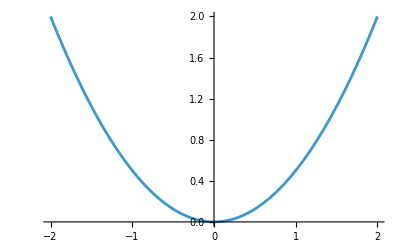
Schrodinger’s equation is not written in terms of forces. It is written in terms of potentials. For a spring with spring constant k, the potential is:

springPotential[x_]:=Module[{k=1},1/2 k x^2]
Plot[springPotential[x],{x,-2,2}]
-Graphics-

You might completely reasonably ask what on Earth this potential has to do with the force F(x)=-kx?

The deep relationship between potentials and forces is that the force is minus the derivative of the potential. Let’s have Mathematica compute the minus the derivative of the above potential for us:

potential[x_]:=1/2 k x^2

-Derivative[1][potential][x]

-k x

Ok, the relationship is as claimed. You are just going to have to accept that Schrodinger used potentials as a way of introducing forces in quantum mechanics. Before Schrodinger, de Broglie and Bohr had made some interesting, crude steps, but neither had written down an equation that could work for real systems like the harmonic oscillator and the hydrogen atom.

If you have a couple of semesters of classical mechanics (one is not quite enough), what Schrodinger did seems entirely reasonable, and even after one semester of classical mechanics it begins to seem reasonable, but it was still a stunning intellectual leap for Schrodinger to combine potentials and second derivatives when writing down the quantum-mechanical equation for the electron.

### Schrodinger Equation for the Harmonic Oscillator

It is common to use the letter ψ for the wave function. Here is the differential equation that ψ satisfies:

-ℏ^2/(2m)Derivative[2][ψ][x]+1/2 kx^2[x]ψ[x]==energy ψ[x]//TraditionalForm

1/2 k x^2(x) ψ(x)-(ℏ^2 ψ''(x))/(2 m)==energy ψ(x)

### Comparison with Wave Equations

Let’s simplify for a moment. The 1/2 k x^2 is unlike anything we have had in a wave equation before. So let’s just set k=0 for a moment and look at what remains:

-ℏ^2/(2m)Derivative[2][ψ][x]==energy ψ[x]//TraditionalForm

-(ℏ^2 ψ''(x))/(2 m)==energy ψ(x)

If energy < 0, this boils down to:

 ψ''(x)∝ψ(x)

That kind of equation is solved by rising or falling exponentials. If energy > 0, this boils down to:

 ψ''(x)∝-ψ(x)

That kind of equation is a wave equation and you know that those are solved by sines and cosines.

Reintroducing the potential term, which near the center of the harmonic oscillator is small and in far away regions is large, causes the Schrodinger equation solutions to look like waves near the center of the harmonic oscillator, and like exponentially-damped (or exponentially-growing) functions far way from the center.

There is an entire semi-rigorous analysis based on the idea in the preceding paragraph, known as the WKB approximation. We are not going to have to study the WKB approximation, because we have Mathematica’s NDSolve[] to do the hard work.

### Units

You can carry around units in Mathematica if you work hard, but typically, we set as many constants as possible to 1, so Mathematica doesn’t have to carry them around symbolically. In the notebook we are about to work on,  I am going to set the constants above (“hbar”, the particle mass, and the spring constant) all equal to one. You might ask why I am not about to set energy=1 as well. The reason is that that overconstrains the problem.

Imagine setting both the radius of a sphere equal to one, and the circumference of that same sphere equal to one. You’d quickly get garbage in whatever problem in which you did that. You can set the radius to one, in which case the circumference is 2π, or you can set the circumference to one, in which case the radius is 1/(2π), but you can’t set them both to one. What we are doing when we set a dimensionful quantity like the radius to one is actually choosing our units of length. We cannot then set some other unrelated or non-trivially related length to one.

When we set ℏ=k=m=1, we are choosing our units of angular momentum, force, and mass. We are then unable to also set energy=1, because the combination ℏ √(k/m) has units of energy.

Note that once again the combination √(k/m) has shown up, and just as we did when we first encountered this combination in the classical harmonic oscillator, we can give it the name ω, in which case our units of energy when we set all these constants to one are ℏω.

### Schrodinger’s Harmonic Oscillator Solution

In fact, the problem we are studying in the previous notebook, while hard, was solved exactly by Schrodinger in 1926.

Let us note, for completeness, that Heisenberg independently solved the harmonic oscillator, but Heisenberg’s approach is unrecognizably different than what we are doing, so I won’t have anything more to say about it.

Here is the beginning of one of Schrodinger’s papers (there are English translations available, but I learned this stuff from modern textbooks, and I have never read the original papers, even in translation, and I am realizing that I would like to, because it might shed light on the otherwise unfathomable intellectual leaps that occurred as people were figuring out quantum mechanics):

-Graphics-

### Where Did Time Go?

You can see in the screenshot above, that there are two versions of Schrodinger’s equation, one with time derivatives, and one without. So far I have only been showing you the one without.

In the real world, even the quantum-mechanical real world, things of course evolve with time. If we have time, I can explain, using the separation of variables trick, the relationship between the two equations.

The equation that I have been showing you and calling the “Schrodinger’s Equation” is, more precisely, known as the “Time-Independent Schrodinger Equation.” It is applicable to a system that has a definite energy, and solving it allows you to discover the allowable energies of the system. A general system, can have a mixture of energies. However, the mixture still only contains mixtures of the set of very definite allowed energies. The allowed energies and the corresponding solutions are usually labeled by an integer n, where n=0, 1, 2, 3, ..., and the n=0 solution is known as the “ground state.”

I will reintroduce time when I get to the interpretation of the Schrodinger equation solutions, ψ_n(x), and we’ll see how combinations of solutions are added together to recover time-dependence.